```mathematica
Needs["GREATER2`"];
```

```mathematica
Hcbm=67.4
```

67.4

```mathematica
Hsnova=74.8
(*Lorentz-Jacobian elliptic eccentricity*)
k=Sqrt[1-(Hcbm/Hsnova)^2]
```

74.8

0.433675

```mathematica
Clear[G,c]
```

```mathematica
(* define our coordinates *)
X =  {t,τ,r,ϕ,θ};
```

```mathematica
(* define a line element Robertson-Walker metric on anti-deSitter *)
ds2 =  c^2*dt^2+c^2*dτ^2 + dr^2/((1-k^2*r^2 )*(1-r^2))+ r^2 dϕ^2+r^2*Sin[ϕ]^2dθ^2;
```

```mathematica
(* calculate metric tensor*)
gdd = Metric[ds2, X]
```

{{c^2,0,0,0,0},{0,c^2,0,0,0},{0,0,5.31706/(5.31706-6.31706 r^2+1. r^4),0,0},{0,0,0,r^2,0},{0,0,0,0,r^2 Sin[ϕ]^2}}

```mathematica
TableForm[gdd]
```

c^2 | 0 | 0 | 0 | 0
0 | c^2 | 0 | 0 | 0
0 | 0 | 5.31706/(5.31706-6.31706 r^2+1. r^4) | 0 | 0
0 | 0 | 0 | r^2 | 0
0 | 0 | 0 | 0 | r^2 Sin[ϕ]^2

```mathematica
Det[gdd]
```

(5.31706 c^4 r^4 Sin[ϕ]^2)/(5.31706-6.31706 r^2+1. r^4)

```mathematica
Tr[gdd]
```

2 c^2+r^2+5.31706/(5.31706-6.31706 r^2+1. r^4)+r^2 Sin[ϕ]^2

```mathematica
(* inverse metric of metric tensor *)
guu =IMetric[gdd];
```

```mathematica
TableForm[guu]
```

1./c^2 | 0. | 0. | 0. | 0.
0. | 1./c^2 | 0. | 0. | 0.
0. | 0. | 1.-1.18807 r^2+0.188074 r^4 | 0. | 0.
0. | 0. | 0. | 1./r^2 | 0.
0. | 0. | 0. | 0. | (1. Csc[ϕ]^2)/r^2

```mathematica
Det[guu]
```

0.+(0.188074 Csc[ϕ]^2)/c^4+(1. Csc[ϕ]^2)/(c^4 r^4)-(1.18807 Csc[ϕ]^2)/(c^4 r^2)

```mathematica
Tr[guu]
```

1.+2./c^2+1./r^2-1.18807 r^2+0.188074 r^4+(1. Csc[ϕ]^2)/r^2

```mathematica
(*Compute the Ricci scalar *)
Rs = SCurvature[gdd, X]
```

(-1.+7.12844 r^2-1.88074 r^4-1. Cot[ϕ]^2+1. Csc[ϕ]^2)/r^2

```mathematica
(* Gaussian curvature:*)
K=Tr[ExtrinsicCurvature[gdd,3, 1, X]]
```

0.-1. (0.+(1. (1. r-1.18807 r^3+0.188074 r^5))/(√(1.-1.18807 r^2+0.188074 r^4)))-(0.+(1.-1.18807 r^2+0.188074 r^4) (-1/(1.-1.18807 r^2+0.188074 r^4)+5.31706/(5.31706-6.31706 r^2+1. r^4))) (0.+((-4.7225×10^-15 r+1.889×10^-14 r^3) (0.+(1.-1.18807 r^2+0.188074 r^4) (-1/(1.-1.18807 r^2+0.188074 r^4)+5.31706/(5.31706-6.31706 r^2+1. r^4))))/(√(1.-1.18807 r^2+0.188074 r^4) (5.31706-6.31706 r^2+1. r^4)^2))-1. (0.+(0.188074 r (5.31706-6.31706 r^2+1. r^4) Sin[ϕ]^2)/(√(1.-1.18807 r^2+0.188074 r^4)))

```mathematica
(* calcxulate full Riemann Curvature tensor*)
Rhijk=Riemann[guu,X];
TableForm[FullSimplify[ExpandAll[Rhijk]]]
```

0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0.-26.5853/(28.2712-67.1765 r^2+50.5394 r^4-12.6341 r^6+1. r^8)+(-84.8135+134.353 r^2)/(r^4 (28.2712-67.1765 r^2+50.5394 r^4-12.6341 r^6+1. r^8))+5.31706/(5.31706 r^4-6.31706 r^6+1. r^8) | 0.
0. | 0. | 0.+26.5853/(28.2712-67.1765 r^2+50.5394 r^4-12.6341 r^6+1. r^8)+(84.8135-134.353 r^2)/(r^4 (28.2712-67.1765 r^2+50.5394 r^4-12.6341 r^6+1. r^8))-5.31706/(5.31706 r^4-6.31706 r^6+1. r^8) | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | ((-56.5423+100.765 r^2-21.2683 r^4) Csc[ϕ]^2)/(r^4 (28.2712-67.1765 r^2+50.5394 r^4-12.6341 r^6+1. r^8))
0. | 0. | 0. | 0. | 0.
0. | 0. | ((56.5423-100.765 r^2+21.2683 r^4) Csc[ϕ]^2)/(r^4 (28.2712-67.1765 r^2+50.5394 r^4-12.6341 r^6+1. r^8)) | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0.+2./r^2-6.31706/(5.31706-6.31706 r^2+1. r^4)+(2. r^2)/(5.31706-6.31706 r^2+1. r^4) | 0.
0. | 0. | 0.-2./r^2+6.31706/(5.31706-6.31706 r^2+1. r^4)-(2. r^2)/(5.31706-6.31706 r^2+1. r^4) | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | Csc[ϕ]^2 (-5.31706/(5.31706 r^4-6.31706 r^6+1. r^8)-1. Cot[ϕ]^2-1. Csc[ϕ]^2)
0. | 0. | 0. | Csc[ϕ]^2 (5.31706/(5.31706 r^4-6.31706 r^6+1. r^8)+1. Cot[ϕ]^2+1. Csc[ϕ]^2) | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.+2./r^2-6.31706/(5.31706-6.31706 r^2+1. r^4)+(2. r^2)/(5.31706-6.31706 r^2+1. r^4)
0. | 0. | 0. | 0. | 0.
0. | 0. | 0.-2./r^2+6.31706/(5.31706-6.31706 r^2+1. r^4)-(2. r^2)/(5.31706-6.31706 r^2+1. r^4) | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 5.31706/(5.31706 r^4-6.31706 r^6+1. r^8)+1. Cot[ϕ]^2+1. Csc[ϕ]^2
0. | 0. | 0. | -5.31706/(5.31706 r^4-6.31706 r^6+1. r^8)-1. Cot[ϕ]^2-1. Csc[ϕ]^2 | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.

```mathematica
(* Ricci tensor contraction*)
Rij=FullSimplify[ExpandAll[TensorContract[TensorTranspose[Rhijk,{4,1,2,3}],{2,1}]]]
```

{{0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.},{0.,0.,(300.639-892.954 r^2+806.164 r^4-235.118 r^6+21.2683 r^8+(300.639-892.954 r^2+806.164 r^4-235.118 r^6+21.2683 r^8) Csc[ϕ]^2)/(r^4 (150.32-535.772 r^2+721.351 r^4-453.614 r^6+135.667 r^8-18.9512 r^10+1. r^12)),0.,0.},{0.,0.,0.,(10.6341 r^2-18.9512 r^4+4. r^6+5.31706 Csc[ϕ]^2+r^4 (7.9756-9.4756 r^2+1.5 r^4+(2.65853-3.15853 r^2+0.5 r^4) Cos[2 ϕ]) Csc[ϕ]^4)/(r^4 (5.31706-6.31706 r^2+1. r^4)),0.},{0.,0.,0.,0.,1. Cot[ϕ]^2+(5.31706+10.6341 r^2-18.9512 r^4+4. r^6+r^4 (5.31706-6.31706 r^2+1. r^4) Csc[ϕ]^2)/(r^4 (5.31706-6.31706 r^2+1. r^4))}}

```mathematica
Tr[Rij]
```

0.+1. Cot[ϕ]^2+(5.31706+10.6341 r^2-18.9512 r^4+4. r^6+r^4 (5.31706-6.31706 r^2+1. r^4) Csc[ϕ]^2)/(r^4 (5.31706-6.31706 r^2+1. r^4))+(300.639-892.954 r^2+806.164 r^4-235.118 r^6+21.2683 r^8+(300.639-892.954 r^2+806.164 r^4-235.118 r^6+21.2683 r^8) Csc[ϕ]^2)/(r^4 (150.32-535.772 r^2+721.351 r^4-453.614 r^6+135.667 r^8-18.9512 r^10+1. r^12))+(10.6341 r^2-18.9512 r^4+4. r^6+5.31706 Csc[ϕ]^2+r^4 (7.9756-9.4756 r^2+1.5 r^4+(2.65853-3.15853 r^2+0.5 r^4) Cos[2 ϕ]) Csc[ϕ]^4)/(r^4 (5.31706-6.31706 r^2+1. r^4))

```mathematica
G=6.732*10^(-8);
c=2.997925*10^(10);
hbar=1.05457266*10^(-27);
```

```mathematica
mplanck=Sqrt[hbar*c/G];
```

```mathematica
(* the Einstein energy density equation without cosmological constant*)
Tij=(-c^5/(4*Pi^2*G^(5/4)*Sqrt[5]))*(Rij-gdd*Rs/2)
```

{{-2.52976×10^59 (0.-(4.49378×10^20 (-1.+7.12844 r^2-1.88074 r^4-1. Cot[ϕ]^2+1. Csc[ϕ]^2))/r^2),0.,0.,0.,0.},{0.,-2.52976×10^59 (0.-(4.49378×10^20 (-1.+7.12844 r^2-1.88074 r^4-1. Cot[ϕ]^2+1. Csc[ϕ]^2))/r^2),0.,0.,0.},{0.,0.,-2.52976×10^59 (-(2.65853 (-1.+7.12844 r^2-1.88074 r^4-1. Cot[ϕ]^2+1. Csc[ϕ]^2))/(r^2 (5.31706-6.31706 r^2+1. r^4))+(300.639-892.954 r^2+806.164 r^4-235.118 r^6+21.2683 r^8+(300.639-892.954 r^2+806.164 r^4-235.118 r^6+21.2683 r^8) Csc[ϕ]^2)/(r^4 (150.32-535.772 r^2+721.351 r^4-453.614 r^6+135.667 r^8-18.9512 r^10+1. r^12))),0.,0.},{0.,0.,0.,-2.52976×10^59 (1/2 (1.-7.12844 r^2+1.88074 r^4+1. Cot[ϕ]^2-1. Csc[ϕ]^2)+(10.6341 r^2-18.9512 r^4+4. r^6+5.31706 Csc[ϕ]^2+r^4 (7.9756-9.4756 r^2+1.5 r^4+(2.65853-3.15853 r^2+0.5 r^4) Cos[2 ϕ]) Csc[ϕ]^4)/(r^4 (5.31706-6.31706 r^2+1. r^4))),0.},{0.,0.,0.,0.,-2.52976×10^59 (1. Cot[ϕ]^2+(5.31706+10.6341 r^2-18.9512 r^4+4. r^6+r^4 (5.31706-6.31706 r^2+1. r^4) Csc[ϕ]^2)/(r^4 (5.31706-6.31706 r^2+1. r^4))-1/2 (-1.+7.12844 r^2-1.88074 r^4-1. Cot[ϕ]^2+1. Csc[ϕ]^2) Sin[ϕ]^2)}}

```mathematica
(*http://en.wikipedia.org/wiki/Weinberg_angle*)
θw0=0.231208;
```

```mathematica
ArcSin[Sqrt[θw0]]
```

0.501614

```mathematica
v=Together[Det[Tij]/.ϕ->ArcSin[Sqrt[θw0]]]
```

-((7.56559596735209×10^338 (-3.79024+1. r^2)^2 (24.4552+48.9104 r^2+99.9238 r^4-224.029 r^6+64.4465 r^8-10.1073 r^10+1. r^12) (24.4552+11.3085 r^2+166.935 r^4-238.173 r^6+64.4465 r^8-10.1073 r^10+1. r^12) (1702.46-7079.25 r^2+10323.2 r^4-5525.13 r^6-709.016 r^8+2047.16 r^10-945.173 r^12+207.497 r^14-22.7414 r^16+1. r^18))/(r^12 (5.31706-6.31706 r^2+1. r^4)^3 (150.32-535.772 r^2+721.351 r^4-453.614 r^6+135.667 r^8-18.9512 r^10+1. r^12)))

```mathematica
w=r/.Solve[Numerator[v]==(c^2/(2*G))^4,r]
```

{-2.30672,-2.30375,-2.30052,-2.28279,-2.13966,-2.02423-1.39778 ⅈ,-2.02423+1.39778 ⅈ,-1.98886+1.41502 ⅈ,-1.98886-1.41502 ⅈ,-1.94694,-1.94681,-1.84634+0.309837 ⅈ,-1.84634-0.309837 ⅈ,-1.05273,-1.0106,-1.,-0.999996,-0.789117,-0.350047-0.4694 ⅈ,-0.350047+0.4694 ⅈ,-0.271969-0.529405 ⅈ,-0.271969+0.529405 ⅈ,0.-1.31128 ⅈ,0.+1.31128 ⅈ,0.271969-0.529405 ⅈ,0.271969+0.529405 ⅈ,0.350047-0.4694 ⅈ,0.350047+0.4694 ⅈ,0.789117,0.999999,1.,1.0106,1.05273,1.84634-0.309837 ⅈ,1.84634+0.309837 ⅈ,1.94683,1.94691,1.98886-1.41502 ⅈ,1.98886+1.41502 ⅈ,2.02423-1.39778 ⅈ,2.02423+1.39778 ⅈ,2.13966,2.28277,2.30035,2.30327,2.30727}

```mathematica
Length[w]
```

46

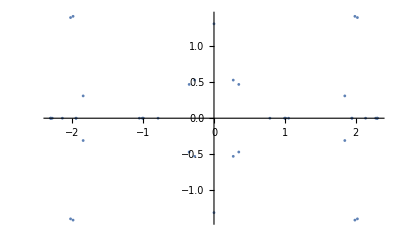

```mathematica
ComplexListPlot[w,ColorFunction->Hue,ImageSize->Full,PlotStyle->PointSize[0.005],PlotRange->All]
```

```mathematica
tt=Tr[Tij]
```

-5.05952×10^59 (0.-(4.49378×10^20 (-1.+7.12844 r^2-1.88074 r^4-1. Cot[ϕ]^2+1. Csc[ϕ]^2))/r^2)-2.52976×10^59 (-(2.65853 (-1.+7.12844 r^2-1.88074 r^4-1. Cot[ϕ]^2+1. Csc[ϕ]^2))/(r^2 (5.31706-6.31706 r^2+1. r^4))+(300.639-892.954 r^2+806.164 r^4-235.118 r^6+21.2683 r^8+(300.639-892.954 r^2+806.164 r^4-235.118 r^6+21.2683 r^8) Csc[ϕ]^2)/(r^4 (150.32-535.772 r^2+721.351 r^4-453.614 r^6+135.667 r^8-18.9512 r^10+1. r^12)))-2.52976×10^59 (1/2 (1.-7.12844 r^2+1.88074 r^4+1. Cot[ϕ]^2-1. Csc[ϕ]^2)+(10.6341 r^2-18.9512 r^4+4. r^6+5.31706 Csc[ϕ]^2+r^4 (7.9756-9.4756 r^2+1.5 r^4+(2.65853-3.15853 r^2+0.5 r^4) Cos[2 ϕ]) Csc[ϕ]^4)/(r^4 (5.31706-6.31706 r^2+1. r^4)))-2.52976×10^59 (1. Cot[ϕ]^2+(5.31706+10.6341 r^2-18.9512 r^4+4. r^6+r^4 (5.31706-6.31706 r^2+1. r^4) Csc[ϕ]^2)/(r^4 (5.31706-6.31706 r^2+1. r^4))-1/2 (-1.+7.12844 r^2-1.88074 r^4-1. Cot[ϕ]^2+1. Csc[ϕ]^2) Sin[ϕ]^2)